# Nihanje

## 1. Defin

## 2. ddfgf

```mathematica
m = 0.5 (* kg - masa telesa *)
g = 9.81 (* m/s^2 - gravitacijski povspesek *)
l = 1.0(* m - dolzina vrvice *)
```

0.5

9.81

1.

```mathematica
t0 = 2 Pi Sqrt[l/g]
```

2.00607

```mathematica
?PolarPlot
```

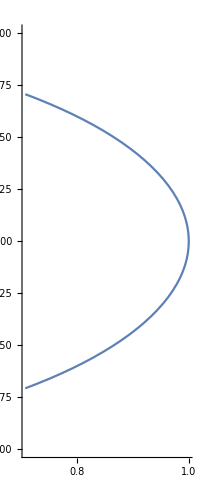

```mathematica
PolarPlot[1,{ϕ,- Pi /4,Pi/4},PlotRange->{-1,1}]
```

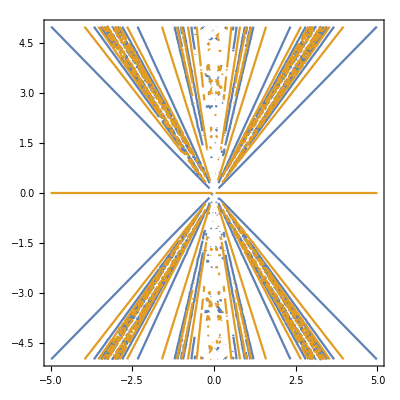

```mathematica
ContourPlot[{l* Cos[Tan[y/x]],l*Sin [Tan[y/x]]},{x,-5,5},{y,-5,5}]
?ParametricPlot
```

```mathematica
NarisiVrv[l_,kot_]:=Line[{{0,l},{Sin[kot]*l,l/2}}]
```

```mathematica
Manipulate[Graphics[NarisiVrv[l,x],Axes->True],{x,-Pi,Pi}]
```

```mathematica
?Line
```

```mathematica
?Manipulate
```